### Mecanismo Manivela-Biela-Corredera

-Graphics-
Figura 1:Diagrama del mecanismo manivela-biela-corredera con sus parámetros cinemáticos

### Parámetros del Mecanismo

```mathematica
ClearAll["Global`*"]; (* limpiar variables *)

l1=4; (* longitud de la manivela*)
l2=10; (* longitud de la biela *)
```

### Ecuaciones de Posición

```mathematica
Eq1=l1 Cos[θ[t]]+l2 Cos[β[t]]==x[t]; (* ecuación eje horizontal *)
Eq2=l1 Sin[θ[t]]+l2 Sin[β[t]]==0; (* ecuación para el eje vertical (z) *)
```

### Ecuaciones de Velocidad (cinématicas)

```mathematica
vE=Dt[{Eq1,Eq2},t,Constants->{l1,l2}]/.{θ[t]->t,θ'[t]->1} (* comando para generar las ecuaciones de velocidad *)
```

{-4 Sin[t]-10 Sin[β[t]] β'[t]==x'[t],4 Cos[t]+10 Cos[β[t]] β'[t]==0}

### Solución numérica

```mathematica
s1=NDSolve[{vE[[1]],vE[[2]],x[0]==14 (*condicion inicial de x *),β[0]==0 (* condicion inicial β *)},{x,β},{t,0,6π}] (* genera la solución numérica *)
```

{{x→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

### Gráficas (visualización)

#### Gráfica de la posición x de la corredera

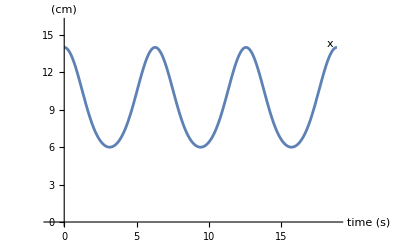

```mathematica
Plot[Evaluate[x[t]/.s1],{t,0,6π},PlotLabels->Placed[{"x"},{6π,Above}],Frame->All,AxesLabel->{"time (s)","(cm)"},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,6π},{0,16}},GridLines->{{2π,4π},{6,14}},ImageSize->400]
```

#### Gráfica de la velocidad x’ de la corredera

```mathematica
xDerivada=D[x[t]/.s1[[1,1]],t]; 
NMaxValue[{xDerivada,0<=t<=2π},t]
```

4.31415

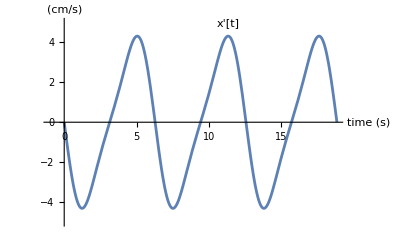

```mathematica
Plot[xDerivada,{t,0,6π},PlotLabels->Placed["x'[t]",Above],Frame->All,AxesLabel->{"time (s)","(cm/s)"},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,6π},{-5,5}},GridLines->{{2π,4π},{4.31,-4.31}},ImageSize->400] (* grafica de velocidad *)
```

```mathematica
N[2π]
```

6.28319

#### Gráfica del Ángulo β

```mathematica
NMaxValue[{β[t]/.s1[[1,2]],0<=t<=2π},t]
```

0.411517

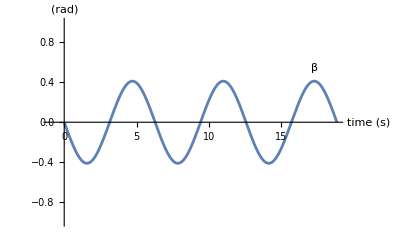

```mathematica
Plot[Evaluate[β[t]/.s1],{t,0,6π},PlotLabels->Placed[{"β"},Above],Frame->All,AxesLabel->{"time (s)","(rad)"},Axes->True,AxesOrigin->{0,0},PlotRange->{{-1,6π},{-1,1}},GridLines->{{2π,4π},{-.41,.41}},ImageSize->400]
```

```mathematica
N[6π]
```

18.8496

### Animación

```mathematica
Animate[
 
eje = Graphics3D[{RGBColor["#FFFF00"](*Amarillo*), Tube[{{0, .1, 0}(*origen tubo*), {0, -.5, 0}(*fin tubo*)}, .125(*radio tubo*)]}];(* eje de motor (shaft)*)

manivela = Graphics3D[{RGBColor["#00FF00"], Tube[{{0, 0, 0}(*origen*), {l1 Cos[t], 0, l1 Sin[t]}(*punto A*)}, .2]}];

pin1 = Graphics3D[{RGBColor["#FFFF00"], Tube[{{l1  Cos[t], .6, l1  Sin[t]}, {l1  Cos[t], -.2, l1  Sin[t]}}, .125]}];

 biela = Graphics3D[{RGBColor["#FF0000"], Tube[{{l1  Cos[t], .4, l1  Sin[t]}(*punto A*), {l1  Cos[t] + l2  Cos[β[t]], .4, l1  Sin[t] + l2  Sin[β[t]]}(* punto B *)}, .2]}] /. s1;(*/. s1 llama a la solución numñerica s1 *)

 pin2 = Graphics3D[{RGBColor["#FFFF00"], Tube[{{l1  Cos[t] + l2  Cos[β[t]], .6, l1  Sin[t] + l2  Sin[β[t]]}, {l1  Cos[t] + l2  Cos[β[t]], -.2, l1  Sin[t] + l2  Sin[β[t]]}}, .125]}] /. s1;

 corredera = Graphics3D[{RGBColor["#00FFFF"], Parallelepiped[{l1  Cos[t] + l2  Cos[β[t]] - 1, -.2, l1  Sin[t] + l2  Sin[β[t]] - .2}(*punto origen del paralelepipedo*), {{2, 0, 0}(*dir X*), {0, .4, 0}(*dir y*), {0, 0, .4}(*dir z*)}]}] /. s1;
 
base = Graphics3D[{RGBColor["#FFFFFF"], Parallelepiped[{5, -.2, -.4}, {{10, 0, 0}, {0, .4, 0}, {0, 0, .2}}]}];
 
 Show[eje,manivela, pin1, biela, pin2, corredera, base, ImageSize -> {500,500}, Axes -> False, Boxed -> False, ViewProjection -> "Orthographic", ViewPoint -> {Top, Right, Front}, PlotRange -> {{-4, 16}(*eje x*), {-1, 1}(*eje y*), {5, -5}(*eje z*)}, Background -> RGBColor["#000000"]], {t, 0, 2 π},AnimationRunning->False,AnimationRepetitions->3,SaveDefinitions->True]
```